## defining model

```mathematica
changepoint=0.451985;
```

```mathematica
λ[t_]:=Piecewise[{{1,t<changepoint},{2,t≥changepoint}}]
```

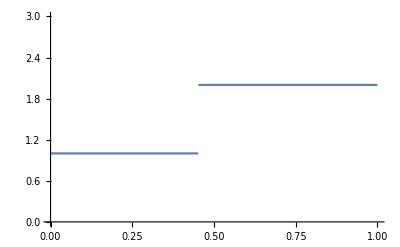

```mathematica
Plot[λ[t],{t,0,1},PlotRange->{0,3}]
```

```mathematica
ts={0,0.095310,0.200671,0.318454,changepoint,0.606136,0.788457,1.011601,1.299283,1.704748,2.397895,Infinity};
```

```mathematica
n=Length[ts]-2;
```

```mathematica
t[i_]:=ts[[i+1]];
```

```mathematica
Omega[t1_,t2_]:=Integrate[1/λ[s],{s,t1,t2}]
```

```mathematica
io[i_]:=Omega[t[i],t[i+1]]
```

```mathematica
(*Pi*)
```

## calculating probabilities and expectations

```mathematica
pi[i_,j_]:=Piecewise[{
{3/2*Exp[-3Omega[0,t[i]]]Exp[-Omega[t[i+1],t[j]]](Exp[-Omega[t[i],t[i+1]]]-Exp[-3Omega[t[i],t[i+1]]])(1-Exp[-Omega[t[j],t[j+1]]]),0<=i<j≤n&&(i∈Integers&&j∈Integers)},
{1/2 Exp[-3Omega[0,t[i]]](2-3Exp[-(t[i+1]-t[i])/λ[t[i]]]+Exp[-3(t[i+1]-t[i])/λ[t[i]]]),
0≤i==j≤n&&(i∈Integers&&j∈Integers)}}]
```

```mathematica
(*Pi is working, at least for constant N [λ]*)
```

```mathematica
(*E[t_3]*)
```

```mathematica
intEt3[i_,j_]:=1/pi[i,j] Integrate[3/(λ[t[i]]λ[t[j]]) t3 Exp[-3Omega[0,t3]]Exp[-Omega[t3,t2]],{t2,t[j],t[j+1]},{t3,t[i],t[i+1]}]
```

```mathematica
Et3[i_,j_]:=Piecewise[{
{3/(4pi[i,j])Exp[-3Omega[0,t[i]]](1-Exp[-Omega[t[j],t[j+1]]])Exp[-Omega[t[i+1],t[j]]]((λ[t[i]]+2t[i])Exp[-Omega[t[i],t[i+1]]]-
(λ[t[i]]+2t[i+1])Exp[-3Omega[t[i],t[i+1]]]),
0<=i<j≤n&&(i∈Integers&&j∈Integers)},
{1/(12pi[i,i])Exp[-3Omega[0,t[i]]](4(3t[i]+λ[t[i]])+
Exp[-3Omega[t[i],t[i+1]]](6t[i+1]+5λ[t[i]])-9Exp[-Omega[t[i],t[i+1]]](2t[i]+λ[t[i]])),
0≤i==j<n&&(i∈Integers&&j∈Integers)},
{t[i]+λ[t[i]]/3.0,i==j==n&&(i∈Integers&&j∈Integers)}
}]
```

```mathematica
(*Et2*)
intEt2[i_,j_]:=1/pi[i,j] Integrate[3/(λ[t[i]]λ[t[j]]) t2 Exp[-3Omega[0,t3]]Exp[-Omega[t3,t2]],{t2,t[j],t[j+1]},{t3,t[i],t[i+1]}]
```

```mathematica
Et2[i_,j_]:=Piecewise[{
{3/(2pi[i,j])Exp[-3Omega[0,t[i]]]Exp[-Omega[t[i+1],t[j]]](Exp[-Omega[t[i],t[i+1]]]-Exp[-3Omega[t[i],t[i+1]]])*
(λ[t[j]]+t[j]-(λ[t[j]]+t[j+1])Exp[-Omega[t[j],t[j+1]]]),
0≤i<j<n&&(i∈Integers&&j∈Integers)},
{3/(2pi[i,j])Exp[-3Omega[0,t[i]]]Exp[-Omega[t[i+1],t[j]]](Exp[-Omega[t[i],t[i+1]]]-Exp[-3Omega[t[i],t[i+1]]])*
(λ[t[j]]+t[j]),
0≤i<j==n&&(i∈Integers&&j∈Integers)},
{1/(6pi[i,j])Exp[-3Omega[0,t[i]]](Exp[-3Omega[t[i],t[i+1]]](3t[i+1]+λ[t[i]])+6t[i]+8λ[t[i]]-9Exp[-Omega[t[i],t[i+1]]](t[i+1]+λ[t[i]])),
0≤i==j<n&&(i∈Integers&&j∈Integers)},
{t[n]+λ[t[n]]/3+λ[t[n]],
i==j==n&&(i∈Integers&&j∈Integers)}
}]
```

## calculating transitions

```mathematica
intqts[i_,j_,k_,l_]:=Piecewise[{
{(*case A*)
Assuming[{s3,s2,t2,t3,u}∈Reals,Integrate[(1/(2s2+s3)Exp[-3Omega[u,s3]]Exp[-2Omega[s3,s2]]*1/λ[t2] Exp[-Omega[s2,t2]])*DiracDelta[t3-Et3[i,j]]/.{s3->Et3[i,j],s2->Et2[i,j]},{u,0,Et3[i,j]},{t2,t[l],t[l+1]},{t3,t[k],t[k+1]}]+Integrate[(2/(2s2+s3)Exp[-2Omega[u,s2]]*1/λ[t2] Exp[-Omega[s2,t2]])*DiracDelta[t3-Et3[i,j]]/.{s3->Et3[i,j],s2->Et2[i,j]},{u,Et3[i,j],Et2[i,j]},{t2,t[l],t[l+1]},{t3,t[k],t[k+1]}]]
,
0≤i==k<j<l&&{i,j,k,l}∈Integers
},
{(*case B*)
Assuming[{s3,s2,t2,t3,u}∈Reals,NIntegrate[(1/(2Et2[i,j]+Et3[i,j])Exp[-3Omega[u,Et3[i,j]]]Exp[-2Omega[Et3[i,j],t2]]*1/λ[t2]),{u,0,Et3[i,j]},{t2,t[l],t[l+1]}]+
NIntegrate[(2/(2Et2[i,j]+Et3[i,j])1/λ[t2] Exp[-2Omega[u,t2]]),{t2,t[l],t[l+1]},{u,Et3[i,j],t2}]],
0≤i==k<l<j&&{i,j,k,l}∈Integers
},
{ (* case C *)
Assuming[{s3,s2,t2,t3,u}∈Reals,NIntegrate[(1/(2Et2[i,j]+Et3[i,j])*2/λ[t3]*Exp[-3Omega[u,t3]]),{t3,t[k],t[k+1]},{u,0,t3}]],
0≤k<i==l<j&&{i,j,k,l}∈Integers
},
{ (* case D *)
Assuming[{s3,s2,t2,t3,u}∈Reals,NIntegrate[(2/(2Et2[i,j]+Et3[i,j])*2/λ[t3]*Exp[-3Omega[u,t3]]),{t3,t[k],t[k+1]},{u,0,t3}]],
0≤k<i<j==l&&{i,j,k,l}∈Integers
},
{ (* case E *)
Assuming[{s3,s2,t2,t3,u}∈Reals,NIntegrate[(2/(2Et2[i,j]+Et3[i,j])*2/λ[t3]*Exp[-3Omega[u,Et3[i,j]]]Exp[-2Omega[Et3[i,j],t3]]),{t3,t[k],t[k+1]},{u,0,Et3[i,j]}]],
0≤i<k<j==l&&{i,j,k,l}∈Integers
},
{ (* case F *)
Assuming[{s3,s2,t2,t3,u}∈Reals,NIntegrate[(2/(2Et2[i,j]+Et3[i,j])*1/λ[t2] Exp[-3Omega[u,Et3[i,j]]]Exp[-2Omega[Et3[i,j],Et2[i,j]]]Exp[-Omega[Et2[i,j],t2]]),{t2,t[l],t[l+1]},{u,0,Et3[i,j]}]],
0≤i<j==k<l&&{i,j,k,l}∈Integers
},
{ (* case G and G2 *)
Assuming[{s3,s2,t2,t3,u}∈Reals,NIntegrate[1/(2Et2[i,j]+Et3[i,j])*1/λ[t2] Exp[-3Omega[u,Et3[i,j]]]Exp[-2Omega[Et3[i,j],t2]],{t2,Et3[i,j],t[l+1]},{u,0,Et3[i,j]}]]+
Assuming[{s3,s2,t2,t3,u}∈Reals,NIntegrate[2/(2Et2[i,j]+Et3[i,j])*1/λ[t2] Exp[-2Omega[u,t2]],{t2,Et3[i,j],t[l+1]},{u,Et3[i,j],t2}]]+
Assuming[{s3,s2,t2,t3,u}∈Reals,NIntegrate[1/(2Et2[i,j]+Et3[i,j])*2/λ[t3] Exp[-3Omega[u,t3]],{t3,t[k],Et3[i,j]},{u,0,t3}]],
0≤i==k==l<j≤n&&{i,j,k,l}∈Integers
},
{ (* case H and H2 *)
Assuming[{s3,s2,t2,t3,u}∈Reals,NIntegrate[2/(2Et2[i,j]+Et3[i,j])*2/λ[t3] Exp[-3Omega[u,Et3[i,j]]]Exp[-2Omega[Et3[i,j],t3]],{t3,t[k],Et2[i,j]},{u,0,Et3[i,j]}]]+
Assuming[{s3,s2,t2,t3,u}∈Reals,NIntegrate[2/(2Et2[i,j]+Et3[i,j])*1/λ[t2] Exp[-3Omega[u,Et3[i,j]]]Exp[-2Omega[Et3[i,j],Et2[i,j]]]*Exp[-Omega[Et2[i,j],t2]],{t2,Et2[i,j],t[k+1]},{u,0,Et3[i,j]}]],
0≤i<k==l==j≤n&&{i,j,k,l}∈Integers
},
{ (* case I and I2 *)
Assuming[{s3,s2,t2,t3,u}∈Reals,NIntegrate[(Exp[-3 Omega[u,Et3[i,j]]] Exp[-2 Omega[Et3[i,j],Et2[i,j]]] Exp[-Omega[Et2[i,j],t2]])/((2 Et2[i,j]+Et3[i,j]) λ[t2]),{t2,t[l],t[l+1]},{u,0,Et3[i,j]}]]+Assuming[{s3,s2,t2,t3,u}∈Reals,NIntegrate[(2 Exp[-2 Omega[u,Et2[i,j]]] Exp[-Omega[Et2[i,j],t2]])/((2 Et2[i,j]+Et3[i,j]) λ[t2]),{t2,t[l],t[l+1]},{u,Et3[i,j],Et2[i,j]}]]+
Assuming[{s3,s2,t2,t3,u}∈Reals,NIntegrate[(2 Exp[-3 Omega[u,Et3[i,j]]] Exp[-2 Omega[Et3[i,j],Et2[i,j]]] Exp[-Omega[Et2[i,j],t2]])/((2 Et2[i,j]+Et3[i,j]) λ[t2]),{t2,t[l],t[l+1]},{u,0,Et3[i,j]}]],
0≤i==j==k<l&&{i,j,k,l}∈Integers
},
{ (* case J and J2 *)
Assuming[{s3,s2,t2,t3,u}∈Reals,NIntegrate[2/(2Et2[i,j]+Et3[i,j])*2/λ[t3] Exp[-3Omega[u,t3]],{t3,t[k],t[k+1]},{u,0,t3}]]+
Assuming[{s3,s2,t2,t3,u}∈Reals,NIntegrate[2/(2Et2[i,j]+Et3[i,j])*1/λ[t3] Exp[-3Omega[u,t3]],{t3,t[k],t[k+1]},{u,0,t3}]],
0≤k<i==j==l&&{i,j,k,l}∈Integers
}
}]
```

```mathematica
qts[i_,j_,k_,l_]:=Piecewise[{
{(* case A *)
1/(2Et2[i,j]+Et3[i,j])1/λ[t[l]] Exp[-2Omega[Et3[i,j],Et2[i,j]]]*(Sum[Exp[-3Omega[t[a+1],Et3[i,j]]](1-Exp[-3io[a]])λ[t[a]]/3,{a,0,i-1}]+(1-Exp[-3(Et3[i,j]-t[i])/λ[t[i]]])*λ[t[i]]/3)*
Exp[-Omega[Et2[i,j],t[l]]]λ[t[l]](1-Exp[-io[l]])+
2/(2Et2[i,j]+Et3[i,j])*1/λ[t[l]]*(Exp[-2Omega[t[i+1],Et2[i,j]]](1-Exp[-2(t[i+1]-Et3[i,j])/λ[t[i]]])*λ[t[i]]/2+
Sum[Exp[-2Omega[t[a+1],Et2[i,j]]](1-Exp[-2io[a]])*λ[t[a]]/2,{a,i+1,j-1}]+(1-Exp[-2(Et2[i,j]-t[j])/λ[t[j]]])*λ[t[j]]/2)Exp[-Omega[Et2[i,j],t[l]]]λ[t[l]](1-Exp[-io[l]]),
0<=i==k<j<l≤n&&{i,j,k,l}∈Integers
},
{ (* case B *)
1/(2Et2[i,j]+Et3[i,j])*1/λ[t[l]]*(Sum[Exp[-3Omega[t[a+1],Et3[i,j]]](1-Exp[-3io[a]])*λ[t[a]]/3,{a,0,i-1}]+(1-Exp[-3(Et3[i,j]-t[i])/λ[t[i]]])*λ[t[i]]/3)*
Exp[-2(*notice the 2*)Omega[Et3[i,j],t[l]]]*λ[t[l]]/2(1-Exp[-2io[l]])+
2/(2Et2[i,j]+Et3[i,j])*1/λ[t[l]]*(1-Exp[-2(t[i+1]-Et3[i,j])/λ[t[i]]])*λ[t[i]]/2*Exp[-2Omega[t[i+1],t[l]]]*λ[t[l]]/2(1-Exp[-2io[l]])+
2/(2Et2[i,j]+Et3[i,j])*1/λ[t[l]](λ[t[l]]/2(1-Exp[-2io[l]])Sum[(1-Exp[-2io[a]])*λ[t[a]]/2 Exp[-2Omega[t[a+1],t[l]]],{a,i+1,l-1}])+
2/(2Et2[i,j]+Et3[i,j])*1/λ[t[l]]*λ[t[l]]/2(t[l+1]-t[l]-λ[t[l]]/2(1-Exp[-2io[l]])),
0<=i==k<l<j≤n&&{i,j,k,l}∈Integers
},
{(* case C *)
1/(2Et2[i,j]+Et3[i,j])*2/λ[t[k]]*(λ[t[k]]/3(1-Exp[-3io[k]])Sum[(1-Exp[-3io[a]])*λ[t[a]]/3 Exp[-3Omega[t[a+1],t[k]]],{a,0,k-1}]+λ[t[k]]/3(t[k+1]-t[k]-λ[t[k]]/3(1-Exp[-3io[k]]))),
0≤k<i==l<j≤n&&{i,j,k,l}∈Integers
},
{ (* case D *)
2/(2Et2[i,j]+Et3[i,j])*2/λ[t[k]]*(λ[t[k]]/3(1-Exp[-3io[k]])Sum[(1-Exp[-3io[a]])*λ[t[a]]/3 Exp[-3Omega[t[a+1],t[k]]],{a,0,k-1}]+λ[t[k]]/3(t[k+1]-t[k]-λ[t[k]]/3(1-Exp[-3io[k]]))),
0≤k<i<j==l≤n&&{i,j,k,l}∈Integers
},
{(* case E *)
2/(2Et2[i,j]+Et3[i,j])*2/λ[t[k]]*(Sum[Exp[-3Omega[t[a+1],Et3[i,j]]](1-Exp[-3io[a]])*λ[t[a]]/3,{a,0,i-1}]+(1-Exp[-3(Et3[i,j]-t[i])/λ[t[i]]])*λ[t[i]]/3)*Exp[-2Omega[Et3[i,j],t[k]]]*λ[t[k]]/2(1-Exp[-2io[k]]),
0≤i<k<j==l&&{i,j,k,l}∈Integers
},
{ (* case F *)
2/(2Et2[i,j]+Et3[i,j])Exp[-2Omega[Et3[i,j],Et2[i,j]]]*1/λ[t[l]]*
(Sum[Exp[-3Omega[t[a+1],Et3[i,j]]]*(1-Exp[-3io[a]])*λ[t[a]]/3,{a,0,i-1}]+(1-Exp[-3(Et3[i,j]-t[i])/λ[t[i]]])*λ[t[i]]/3)Exp[-Omega[Et2[i,j],t[l]]]λ[t[l]](1-Exp[-io[l]]),
0≤i<j==k<l&&{i,j,k,l}∈Integers
},
{ (* case G and G2 *)
1/(2Et2[i,j]+Et3[i,j])*(1/λ[t[k]]*(Sum[Exp[-3Omega[t[a+1],Et3[i,j]]](1-Exp[-3io[a]])*λ[t[a]]/3,{a,0,i-1}]+(1-Exp[-3(Et3[i,j]-t[i])/λ[t[i]]])*λ[t[i]]/3)*λ[t[k]]/2*
(1-Exp[-2(t[k+1]-Et3[i,j])/λ[t[k]]])+t[k+1]-Et3[i,j]-λ[t[k]]/2(1-Exp[-2(t[k+1]-Et3[i,j])/λ[t[k]]]))+
1/(2Et2[i,j]+Et3[i,j])*2/λ[t[k]](Sum[(1-Exp[-3io[a]])*λ[t[a]]/3*Exp[-3Omega[t[a+1],t[k]]],{a,0,k-1}]*λ[t[k]]/3(1-Exp[-3(Et3[i,j]-t[k])/λ[t[k]]])+λ[t[k]]/3(Et3[i,j]-t[k]-λ[t[k]]/3(1-Exp[-3(Et3[i,j]-t[k])/λ[t[k]]]))),
0≤i==k==l<j≤n&&{i,j,k,l}∈Integers
},
{ (* case H and H2 *)
1/(2Et2[i,j]+Et3[i,j])*4/λ[t[k]]*Exp[-2Omega[Et3[i,j],t[k]]](Sum[Exp[-3Omega[t[a+1],Et3[i,j]]]*(1-Exp[-3io[a]])*λ[t[a]]/3,{a,0,i-1}]+(1-Exp[-3(Et3[i,j]-t[i])/λ[t[i]]])*λ[t[i]]/3)*
λ[t[k]]/2(1-Exp[-2(Et2[i,j]-t[k])/λ[t[k]]])+
2/(2Et2[i,j]+Et3[i,j])*1/λ[t[k]] Exp[-2Omega[Et3[i,j],Et2[i,j]]]*(Sum[Exp[-3Omega[t[a+1],Et3[i,j]]](1-Exp[-3io[a]])*λ[t[a]]/3,{a,0,i-1}]+
(1-Exp[-3(Et3[i,j]-t[i])/λ[t[i]]])*λ[t[i]]/3)*λ[t[k]](1-Exp[-(t[k+1]-Et2[i,j])/λ[t[k]]]),
0≤i<k==l==j&&{i,j,k,l}∈Integers
},
{ (* case I and I2 *)
1/(2 Et2[i,j]+Et3[i,j])(1/λ[t[l]] Exp[-2 Omega[Et3[i,j],Et2[i,j]]] (∑_(a=0)^(i-1) 1/3 Exp[-3 Omega[t[a+1],Et3[i,j]]] (1-Exp[-3 io[a]]) λ[t[a]]+1/3 (1-Exp[-(3 (Et3[i,j]-t[i]))/λ[t[i]]]) λ[t[i]]) Exp[-Omega[Et2[i,j],t[l]]] λ[t[l]] (1-Exp[-io[l]])+1/(λ[t[l]] 2)2 λ[t[i]] (1-Exp[-(2 (Et2[i,j]-Et3[i,j]))/λ[t[i]]]) Exp[-Omega[Et2[i,j],t[l]]] λ[t[l]] (1-Exp[-io[l]]))+
1/((2 Et2[i,j]+Et3[i,j]) λ[t[l]])2 Exp[-2 Omega[Et3[i,j],Et2[i,j]]] Exp[-Omega[Et2[i,j],t[l]]] λ[t[l]] (1-Exp[-io[l]]) (∑_(a=0)^(i-1) 1/3 Exp[-3 Omega[t[a+1],Et3[i,j]]] (1-Exp[-3 io[a]]) λ[t[a]]+1/3 (1-Exp[-(3 (Et3[i,j]-t[i]))/λ[t[i]]]) λ[t[i]]),

0≤i==j==k<l&&{i,j,k,l}∈Integers
},
{ (* case J and J2 *)
2/(2Et2[i,j]+Et3[i,j])*2/λ[t[k]](λ[t[k]]/3(1-Exp[-3io[k]])(Sum[(1-Exp[-3io[a]])λ[t[a]]/3 Exp[-3Omega[t[a+1],t[k]]],{a,0,k-1}])+λ[t[k]]/3*
(t[k+1]-t[k]-λ[t[k]]/3(1-Exp[-3io[k]])))+
2/(2Et2[i,j]+Et3[i,j])1/λ[t[k]](Sum[(1-Exp[-3io[a]])λ[t[a]]/3 Exp[-3Omega[t[a+1],t[k]]],{a,0,k-1}] λ[t[k]]/3(1-Exp[-3io[k]])+
λ[t[k]]/3(t[k+1]-t[k]-λ[t[k]]/3(1-Exp[-3io[k]]))),
0≤k<i==j==l&&{i,j,k,l}∈Integers
}
}]
```

## exporting

```mathematica
numStates = (n+1)(n+2)/2
```

66

```mathematica
getIndex[i_,j_,n_]:=i*n-i(i-1)/2+j+1;
```

```mathematica
allqts = Table[0,{i,1,numStates},{j,1,numStates}];
```

```mathematica
For[i=0,i≤n,i++,
Print[i];
For[j=i,j≤n,j++,
For[k=0,k≤n,k++,
For[l=k,l≤n,l++,
ijIdx = getIndex[i,j,n];
klIdx=getIndex[k,l,n];
allqts[[ijIdx,klIdx]]=qts[i,j,k,l];
]
]
]
]
```

0

1

2

3

4

5

6

7

8

9

10

```mathematica
Export["mathematica_qtsprobs.csv",allqts]
```

mathematica_qtsprobs.csv

```mathematica
allintqts = Table[0,{i,1,numStates},{j,1,numStates}];
```

```mathematica
For[i=0,i≤n,i++,
Print[i];
For[j=i,j≤n,j++,
For[k=0,k≤n,k++,
For[l=k,l≤n,l++,
ijIdx = getIndex[i,j,n];
klIdx=getIndex[k,l,n];
allintqts[[ijIdx,klIdx]]=intqts[i,j,k,l];
]
]
]
]
```

0

1

2

3

4

5

6

7

8

9

10

```mathematica
Export["mathematica_intqtsprobs.csv",allintqts]
```

mathematica_intqtsprobs.csv

```mathematica
pts[i_,j_,k_,l_,ρ_]:=
```

## making pts transitions

```mathematica
pts[i_,j_,k_,l_,ρ_]:=Module[{treeSize, probRecomb},treeSize=3*Et3[i,j]+2*(Et2[i,j]-Et3[i,j]); probRecomb=1-Exp[-treeSize*ρ/2];qts[i,j,k,l]*probRecomb]
```

```mathematica
pts[4,4,2,4,0.0001]
```

6.34354×10^-6

## emission probabilities

```mathematica
emit[k_,i_,j_,Td_,θ_]:=Piecewise[{
{
Exp[(-θ(2Et2[i,j]+Et3[i,j]+3Td))/2],
k==0
},
{
Exp[-θ/2*(Et2[i,j]-Et3[i,j])](1-Exp[-θ/2(2Et3[i,j]+Et2[i,j]+3Td)]),
k==1
},
{
(1-Exp[-θ/2(Et2[i,j]-Et3[i,j])])Exp[-θ/2(2Et3[i,j]+Et2[i,j]+3Td)],
k==2
},
{
(1-Exp[-θ/2(Et2[i,j]-Et3[i,j])])(1-Exp[-θ/2(2Et3[i,j]+Et2[i,j]+3Td)]),
k==3
}
}]
```

```mathematica
emit[3,2,4,0,0.01]
```

7.03557×10^-6

```mathematica
ρ=0.001;θ=0.001;Td = 0.2;
```

```mathematica
Table[emit[x,10,10,Td,θ],{x,{0,1,2,3}}]
```

{0.993127,0.00587361,0.000993624,5.87655×10^-6}

```mathematica
?emit
```

Global`emit

emit[k_,i_,j_,Td_,θ_]:=Piecewise[{{Exp[1/2 (-θ) (2 Et2[i,j]+Et3[i,j]+3 Td)],k==0},{Exp[1/2 (-θ) (Et2[i,j]-Et3[i,j])] (1-Exp[1/2 (-θ) (2 Et3[i,j]+Et2[i,j]+3 Td)]),k==1},{(1-Exp[1/2 (-θ) (Et2[i,j]-Et3[i,j])]) Exp[1/2 (-θ) (2 Et3[i,j]+Et2[i,j]+3 Td)],k==2},{(1-Exp[1/2 (-θ) (Et2[i,j]-Et3[i,j])]) (1-Exp[1/2 (-θ) (2 Et3[i,j]+Et2[i,j]+3 Td)]),k==3}}]